FittedModel[0.0113962+0.014985 ⅇ^(-1.04384 (x-«18»)^2)+0.0178482 ⅇ^(-1.50471 (x-2.25197)^2)]

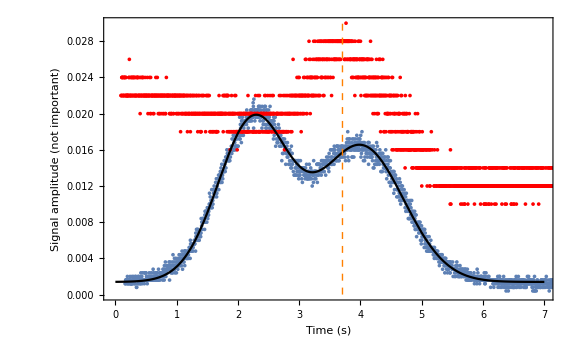

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.0178482 | 0.000051619 | 345.768 | 2.67190360829×10^-1615
B | 1.50471 | 0.0144793 | 103.922 | 8.75642115457×10^-752
CC | 2.25197 | 0.00325079 | 692.745 | 3.48624351783×10^-2140
DD | 0.014985 | 0.0000450774 | 332.427 | 8.56538288497×10^-1586
EE | 1.04384 | 0.0123615 | 84.4423 | 3.69915915201×10^-620
FF | 4.01358 | 0.00431047 | 931.124 | 1.038120285×10^-2364
GG | 0.0113962 | 0.0000249813 | 456.187 | 6.11342741021×10^-1824

{3.706,0.05,Single peak with manual error}

{2.25197,0.00325079,First MOT visibility peak with error}

{4.01358,0.00431047,Second MOT visibility peak with error}

{1.76162,0.00539887,Time difference between two peaks with error}

{17.9948,0.0551492,s/MHz conversion factor with error}

{0.307583,0.0501855,Detuning in seconds with error}

{5.53491,0.903238,Detuning frequency in MHz with error}

```mathematica
SetDirectory[NotebookDirectory[]];
las2=Drop[Import["../osc/ALL0004/F0004CH1.CSV", {"Data", All, {4,5}}],-700];
pd2 = Drop[Drop[Import["../osc/ALL0004/F0004CH2.CSV",{"Data",All,{4,5}}],40],-700];
manualErrorBar = "Plot[0.031,{x,3.706-0.05,3.706+0.05},PlotStyle→{Black,Thick}],";
gg = NonlinearModelFit[pd2, A*Exp[-B*(x-CC)^2]+DD*Exp[-EE*(x-FF)^2]+GG,{{A, 0.015},B,{CC,2.344},{DD, 0.010},EE,{FF, 3.986},{GG, 0.0012}},x]
Show[ListPlot[Map[{#[[1]],#[[2]]-0.01}&,pd2]],ListPlot[Map[{#[[1]],(#[[2]]-10.75) *0.1+0.005}&,las2],PlotStyle->Red],
Plot[gg[x]-0.01,{x,0,7},PlotStyle->{Black}],

Graphics[{Orange,Dashed, Thin,Line[{{3.706,0},{3.706,0.035}}]}],


PlotRange->{{-0.05, 7},{0,0.03}},Frame -> {{False, False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Signal amplitude (not important)",Medium]},ImageSize->Large]
gg["ParameterTable"]
ts2 = TimeSeries[pd2];
ts3 = TimeSeries[las2];
singlePeak = {FindPeaks[ts3,100]["PathTimes"][[2]], 0.05, "Single peak with manual error"}
t1 ={ CC/.gg["BestFitParameters"],gg["ParameterErrors"][[3]], "First MOT visibility peak with error"}
t2 ={ FF/.gg["BestFitParameters"],gg["ParameterErrors"][[6]], "Second MOT visibility peak with error"}
theoreticalFreqDiff = {31.7, "MHz"};
timeDiff = {Abs[t1[[1]]-t2[[1]]], Sqrt[t1[[2]]^2 + t2[[2]]^2], "Time difference between two peaks with error"}
sToMHz = {theoreticalFreqDiff[[1]]/timeDiff[[1]], theoreticalFreqDiff[[1]]/timeDiff[[1]]^2 * timeDiff[[2]], "s/MHz conversion factor with error"}
detuningTime = {Abs[singlePeak[[1]]-t2[[1]]],Sqrt[singlePeak[[2]]^2 + t2[[2]]^2], "Detuning in seconds with error"}
detuningFrequency = {detuningTime[[1]]*sToMHz[[1]], Sqrt[detuningTime[[1]]^2*sToMHz[[2]]^2 + detuningTime[[2]]^2 *sToMHz[[1]]^2], "Detuning frequency in MHz with error"}
```

```mathematica
Show[ListPlot[Map[{#[[1]],#[[2]]-0.01}&,pd2]],ListPlot[Map[{#[[1]],(#[[2]]-10.75) *0.1+0.005}&,las2],PlotStyle->Red],
Plot[gg[x]-0.01,{x,0,7},PlotStyle->{Black}],

Graphics[{Orange,Dashed, Thin,Line[{{3.706,0},{3.706,0.035}}]}],


PlotRange->{{-0.05, 7},{0,0.03}},Frame -> {{True, False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Signal amplitude (not important)",Medium]},ImageSize->Large]
```

-Graphics-

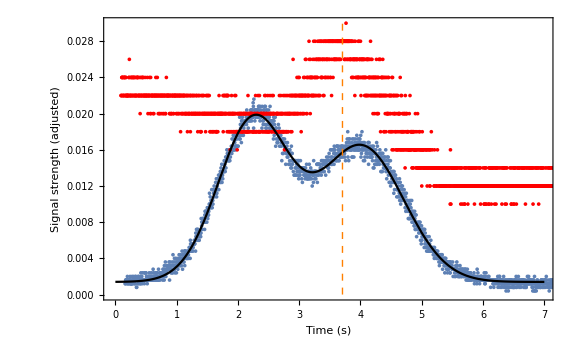

```mathematica
Show[ListPlot[Map[{#[[1]],#[[2]]-0.01}&,pd2]],ListPlot[Map[{#[[1]],(#[[2]]-10.75) *0.1+0.005}&,las2],PlotStyle->Red],
Plot[gg[x]-0.01,{x,0,7},PlotStyle->{Black}],

Graphics[{Orange,Dashed, Thin,Line[{{3.706,0},{3.706,0.035}}]}],


PlotRange->{{-0.05, 7},{0,0.03}},Frame -> {{True, False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Signal strength (adjusted)",Medium]},ImageSize->Large]
```